```mathematica
ClearAll["Global`*"]
detg:=NN[r]*r^3
coordenadasU:={t,r,θ,ϕ,γ}
len:=Length[coordenadasU]
ee:={{NN[r]*Sqrt[f[r]],0,0,0,0},{0,1/Sqrt[f[r]],0,0,0},{0,0,r,0,0},{0,0,0, r*Sin[θ],0},{0,0,0,0, r*Sin[θ]*Sin[ϕ]}};
eei=Inverse[ee];
nn={{-1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
```

```mathematica
For[j=0,j<len,j++,For[i=0,i<len,i++,edown[i,j]=ee⟦i+1⟧⟦j+1⟧;]]
For[j=0,j<len,j++,For[i=0,i<len,i++,eup[i,j]=eei⟦i+1⟧⟦j+1⟧;]]
For[j=0,j<len,j++,For[i=0,i<len,i++,η[i,j]=nn⟦i+1⟧⟦j+1⟧;]]

r1={x[0]->t};
r2={x[1]->r};
r3={x[2]->θ};
r4={x[3]->ϕ};
r5={x[4]->γ};
```

```mathematica
edown[0,0]
```

√f[r] NN[r]

### Definitions of g_(μ ν) , g^(μ ν)

```mathematica
(* g_{μν}=η_{AB} e^A_{μ} e^B_{ν} *)
ClearAll[μ,ν,ρ,σ,A,B]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
gdown[μ,ν]=Simplify[Sum[Sum[η[A,B]edown[A,μ]edown[B,ν],{A,0,len-1}],{B,0,len-1}]];
]
]

(* g^{μν}= η^{AB} e_A^{μ} e_B^{ν} = = η_{AB} e_A^{μ} e_B^{ν} *)
ClearAll[μ,ν,ρ,σ,A,B]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
gup[μ,ν]=Sum[Sum[η[A,B]eup[A,μ]eup[B,ν],{A,0,len-1}],{B,0,len-1}];
]
]
```

```mathematica
gdown[0,0]
```

-f[r] NN[r]^2

### Christoffel’s symbols → Γ_(μ ν)^ρ=Γ[ρ,μ,ν]

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[ρ=0,ρ<len,ρ++,
Γ[ρ,μ,ν]=Simplify[Series[1/2 *Sum[gup[ρ,σ] (D[gdown[ν,σ],x[μ]/.r1/.r2/.r3/.r4/.r5]+D[gdown[σ,μ],x[ν]/.r1/.r2/.r3/.r4/.r5]-D[gdown[μ,ν],x[σ]/.r1/.r2/.r3/.r4]/.r5),{σ,0,len-1}],{ϵ,0,2}]];
]
]
]
```

```mathematica
Γ[3,4,4]
```

-Cos[ϕ] Sin[ϕ]

### Funciones

```mathematica
Clear[A,B,CC,ψ]
A[r_]:=(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])/(2 NN[r])
B[r_]:=-(NN[r] f'[r]+2 f[r] NN'[r])/(2 r NN[r])
CC[r_]:=-f'[r]/(2r)
ψ[r_]:=(1-f[r])/r^2
```

### Eta

```mathematica
eta:=DiagonalMatrix[{-1,1,1,1,1}]
len:=Length[eta]
For[j=0,j<len,j++,For[i=0,i<len,i++,η[i,j]=eta⟦i+1⟧⟦j+1⟧;]]
```

### Proyectores

```mathematica
delta[a_,b_]:=KroneckerDelta[a,b]
tau[a_,b_]:=delta[a,0]*delta[0,b]
rho[a_,b_]:=delta[a,1]*delta[1,b]
sigma[a_,b_]:=delta[a,2]*delta[2,b]+delta[a,3]*delta[3,b]+delta[a,4]*delta[4,b]
```

### Riemann Tensor

```mathematica
RUUDD0[a_,b_,c_,d_]:=2*(-A[r]*2*tau[c,a]*rho[d,b]+B[r]*2*tau[c,a]*sigma[d,b]+CC[r]*2*rho[c,a]*sigma[d,b]+ψ[r]*sigma[c,a]*sigma[d,b])
RUUDD[a_,b_,c_,d_]:=1/8 (RUUDD0[a,b,c,d]-RUUDD0[b,a,c,d]-RUUDD0[a,b,d,c]+RUUDD0[b,a,d,c]+RUUDD0[c,d,a,b]-RUUDD0[d,c,a,b]-RUUDD0[c,d,b,a]+RUUDD0[d,c,b,a])
RUUUD[a_,b_,c_,d_]:=Sum[η[c,e]*RUUDD[a,b,e,d],{e,0,len-1}]
RUDDD[a_,b_,c_,d_]:=Sum[η[b,e]*RUUDD[a,e,c,d],{e,0,len-1}]
RUUUU[a_,b_,c_,d_]:=Sum[η[d,g]*η[c,e]*RUUDD[a,b,e,g],{e,0,len-1},{g,0,len-1}]
RDDDD[a_,b_,c_,d_]:=Sum[η[b,g]*η[a,e]*RUUDD[e,g,c,d],{e,0,len-1},{g,0,len-1}]
RDUDU[a_,b_,c_,d_]:=Sum[η[d,g]*η[a,e]*RUUDD[e,b,c,g],{e,0,len-1},{g,0,len-1}]
```

### Ricci Tensor

```mathematica
RDD[a_,b_]:=Simplify[Sum[RUDDD[c,a,c,b],{c,0,len-1}]]
RDU[a_,b_]:=Sum[η[b,c]*RDD[a,c],{c,0,len-1}]
RUU[a_,b_]:=Sum[η[a,c]*RDU[c,b],{c,0,len-1}]
```

### Ricci Scalar

```mathematica
R:=Simplify[Sum[RDU[a,a],{a,0,len-1}]]
```

```mathematica
R
```

-1/(r^2 NN[r])(NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r])))

### Derivada Covariante

```mathematica
Clear[d]
```

```mathematica
CovDRDD[a_,b_,c_]:=D[RDD[b,c],coordenadasU[[a+1]]]-Sum[Γ[d,a,b]*RDD[d,c]-Γ[d,a,c]*RDD[b,d],{d,0,len-1}]
```

```mathematica
CovDRDD[1,3,3]
```

(2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r]))/(r^3 NN[r])+(NN'[r] (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r]))/(r^2 NN[r]^2)-1/(r^2 NN[r])(f[r] NN'[r]+r f'[r] NN'[r]+(-2+2 f[r]+r f'[r]) NN'[r]+NN[r] (3 f'[r]+r f''[r])+r f[r] NN''[r])

```mathematica
CovDRDD[0,0,1]
```

1/(2 r NN[r])(f'[r]/(2 f[r])+NN'[r]/NN[r]) (3 NN[r] f'[r]+6 f[r] NN'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])-1/2 f[r] NN[r] (NN[r] f'[r]+2 f[r] NN'[r]) (-(3 f'[r])/(2 r)-(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])/(2 NN[r]))

```mathematica
CovDRUU[a_,b_,c_]:=D[RUU[b,c],coordenadasU[[a+1]]]-Sum[Γ[d,a,b]*RUU[d,c]-Γ[d,a,c]*RUU[b,d],{d,0,len-1}]
```

```mathematica
CovDRUU[4,1,4]
```

(NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])/(r^3 NN[r])-r f[r] Sin[θ]^2 Sin[ϕ]^2 (-(3 f'[r])/(2 r)-(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])/(2 NN[r]))

```mathematica
I9=Sum[Sum[Sum[CovDRDD[a,b,c]*CovDRUU[a,b,c],{a,0,len-1}],{b,0,len-1}],{c,0,len-1}]
```

$Aborted

```mathematica
Simplify[I9]
```

1/(2 r^2 f[r]^2 NN[r]^2)(1/4 r^2 (-5 Cos[θ]+Cos[3 θ])^2 Csc[θ]^2 f[r]^2 NN[r]^2 (B[r]+CC[r]+2 ψ[r])^2+1/4 r^2 (-5 Cos[ϕ]+Cos[3 ϕ])^2 Csc[ϕ]^2 f[r]^2 NN[r]^2 (B[r]+CC[r]+2 ψ[r])^2+4 r^2 f[r]^2 NN[r]^2 (Cot[θ]+Cos[θ] Sin[θ] Sin[ϕ]^2)^2 (B[r]+CC[r]+2 ψ[r])^2+4 f[r]^2 NN[r]^2 (B[r]+CC[r]-r^2 (A[r]-3 CC[r]) f[r]+2 ψ[r])^2+4 f[r]^2 NN[r]^2 (B[r]+CC[r]-r^2 (A[r]-3 CC[r]) f[r] Sin[θ]^2+2 ψ[r])^2+4 f[r]^2 NN[r]^2 (B[r]+CC[r]-r^2 (A[r]-3 CC[r]) f[r] Sin[θ]^2 Sin[ϕ]^2+2 ψ[r])^2+2 r^2 f[r]^2 NN[r]^2 (A'[r]-3 B'[r])^2+2 r^2 f[r]^2 NN[r]^2 (A'[r]-3 CC'[r])^2+r^2 (A[r]-3 B[r]+(A[r]-3 CC[r]) f[r]^2 NN[r]^2)^2 (NN[r] f'[r]+2 f[r] NN'[r])^2+6 r^2 f[r]^2 NN[r]^2 (B'[r]+CC'[r]+2 ψ'[r])^2)

```mathematica
I10=Simplify[Sum[Sum[gup[a,d]*D[R,coordenadasU[[a+1]]]*D[R,coordenadasU[[d+1]]],{a,1,len-1}],{d,0,len-1}]]
```

1/(r^6 NN[r]^4)f[r] (-r^2 NN'[r] (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r]))+NN[r]^2 (12-12 f[r]+6 r^2 f''[r]+r^3 f^(3)[r])+r NN[r] (r (3 r NN'[r] f''[r]+f'[r] (6 NN'[r]+5 r NN''[r]))+f[r] (-6 NN'[r]+2 r (3 NN''[r]+r NN^(3)[r]))))^2

## Curvatura n=1

```mathematica
L1=Collect[Expand[R*detg],{NN[r],NN'[r],NN''[r]}]
```

(-6 r^2 f[r]-3 r^3 f'[r]) NN'[r]+NN[r] (6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r])-2 r^3 f[r] NN''[r]

## Curvatura n=2

```mathematica
L2=Collect[Expand[(detg/((len-2)*(len-3)))*(R^2-4*Sum[RDD[a,b]*RUU[a,b],{a,0,len-1},{b,0,len-1}]+Sum[RDDDD[a,b,c,d]*RUUUU[a,b,c,d],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1}])],{NN[r],NN'[r],NN''[r]}]
```

(-4 f[r]+4 f[r]^2-6 r f'[r]+10 r f[r] f'[r]) NN'[r]+NN[r] (-4 f'[r]+4 f[r] f'[r]+2 r f'[r]^2-2 r f''[r]+2 r f[r] f''[r])+(-4 r f[r]+4 r f[r]^2) NN''[r]

## Curvatura n=3

### Invariantes

```mathematica
I1=Simplify[R^3]
```

-((NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r])))^3)/(r^6 NN[r]^3)

```mathematica
I2=Simplify[Sum[RDU[a,c]*RDU[c,b]*RDU[b,a],{a,0,len-1},{b,0,len-1},{c,0,len-1}]]
```

-(24 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])^3+r^3 (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])^3+r^3 (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))^3)/(8 r^6 NN[r]^3)

```mathematica
I3=Simplify[Sum[RUU[a,b]*RUU[c,d]*RDDDD[a,c,b,d],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1}]]
```

1/(2 r^6 NN[r]^3)(12 (1-f[r]) NN[r] (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])^2-3 r^2 (NN[r] f'[r]+2 f[r] NN'[r]) (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r]) (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))-1/2 r^4 (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r]) (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r]) (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))+3 r^2 NN[r] f'[r] (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r]) (-3 NN[r] f'[r]-r (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])))

```mathematica
I4=Simplify[Sum[RDDDD[a,c,b,d]*RUUUD[a,c,b,e]*RUU[d,e],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1},{e,0,len-1}]]
```

-1/(4 r^6 NN[r]^3)(48 (-1+f[r])^2 NN[r]^2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])+6 r^2 NN[r]^2 f'[r]^2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])+6 r^2 (NN[r] f'[r]+2 f[r] NN'[r])^2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])+3 r^3 NN[r]^2 f'[r]^2 (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])+r^5 (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2 (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])+3 r^3 (NN[r] f'[r]+2 f[r] NN'[r])^2 (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))+r^5 (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2 (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r])))

```mathematica
I5=Simplify[Sum[RDU[a,c]*RDU[c,a]*R,{a,0,len-1},{c,0,len-1}]]
```

-1/(2 r^6 NN[r]^3)(NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r]))) (NN[r]^2 (24+24 f[r]^2+15 r^2 f'[r]^2+24 f[r] (-2+r f'[r])+r^4 f''[r]^2+6 r f'[r] (-4+r^2 f''[r]))+2 r NN[r] (12 f[r]^2 NN'[r]+3 r^2 f'[r] NN'[r] (3 f'[r]+r f''[r])+f[r] (3 NN'[r] (-4+5 r f'[r]+r^2 f''[r])+2 r^2 (3 f'[r]+r f''[r]) NN''[r]))+r^2 (9 r^2 f'[r]^2 NN'[r]^2+6 r f[r] f'[r] NN'[r] (3 NN'[r]+2 r NN''[r])+4 f[r]^2 (6 NN'[r]^2+3 r NN'[r] NN''[r]+r^2 NN''[r]^2)))

```mathematica
I6=Simplify[Sum[RDDDD[a,b,c,d]*RUUUU[a,b,c,d],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1}]*R]
```

-1/(r^2 NN[r])((12 (-1+f[r])^2)/r^4+(3 f'[r]^2)/r^2+(3 (NN[r] f'[r]+2 f[r] NN'[r])^2)/(r^2 NN[r]^2)+(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2/NN[r]^2) (NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r])))

```mathematica
I7=Simplify[Sum[RDUDU[a,b,c,d]*RDUDU[b,e,d,g]*RDUDU[e,a,g,c],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1},{e,0,len-1},{g,0,len-1}]]
```

1/(4 r^6)3 (-8 (-1+f[r])^3-6 r^2 (-1+f[r]) f'[r]^2-(6 r^2 (-1+f[r]) (NN[r] f'[r]+2 f[r] NN'[r])^2)/NN[r]^2-(3 r^4 f'[r] (NN[r] f'[r]+2 f[r] NN'[r]) (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r]))/NN[r]^2)

```mathematica
I8=Simplify[Sum[RUUDD[a,b,c,d]*RUUDD[c,d,e,g]*RUUDD[e,g,a,b],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1},{e,0,len-1},{g,0,len-1}]]
```

-(24 (-1+f[r])^3)/r^6-(3 f'[r]^3)/r^3-(3 (NN[r] f'[r]+2 f[r] NN'[r])^3)/(r^3 NN[r]^3)-(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^3/NN[r]^3

```mathematica
L3=(7/12)*(I7+(21/56) I6-(33/14) I5-(9/7) I4+(15/7) I3+(18/7) I2+(15/56) I1)*detg
```

7/12 r^3 NN[r] (1/(4 r^6)3 (-8 (-1+f[r])^3-6 r^2 (-1+f[r]) f'[r]^2-(6 r^2 (-1+f[r]) (NN[r] f'[r]+2 f[r] NN'[r])^2)/NN[r]^2-1/NN[r]^2 3 r^4 f'[r] (NN[r] f'[r]+2 f[r] NN'[r]) (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r]))-1/(8 r^2 NN[r])3 ((12 (-1+f[r])^2)/r^4+(3 f'[r]^2)/r^2+(3 (NN[r] f'[r]+2 f[r] NN'[r])^2)/(r^2 NN[r]^2)+(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2/NN[r]^2) (NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r])))-1/(56 r^6 NN[r]^3)15 (NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r])))^3+1/(28 r^6 NN[r]^3)9 (48 (-1+f[r])^2 NN[r]^2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])+6 r^2 NN[r]^2 f'[r]^2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])+6 r^2 (NN[r] f'[r]+2 f[r] NN'[r])^2 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])+3 r^3 NN[r]^2 f'[r]^2 (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])+r^5 (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2 (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])+3 r^3 (NN[r] f'[r]+2 f[r] NN'[r])^2 (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))+r^5 (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2 (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r])))-1/(28 r^6 NN[r]^3)9 (24 (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])^3+r^3 (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r])^3+r^3 (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))^3)+1/(14 r^6 NN[r]^3)15 (12 (1-f[r]) NN[r] (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r])^2-3 r^2 (NN[r] f'[r]+2 f[r] NN'[r]) (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r]) (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))-1/2 r^4 (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r]) (3 NN[r] f'[r]+3 r f'[r] NN'[r]+r NN[r] f''[r]+2 r f[r] NN''[r]) (3 r f'[r] NN'[r]+NN[r] (3 f'[r]+r f''[r])+2 f[r] (3 NN'[r]+r NN''[r]))+3 r^2 NN[r] f'[r] (NN[r] (-2+2 f[r]+r f'[r])+r f[r] NN'[r]) (-3 NN[r] f'[r]-r (3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])))+1/(28 r^6 NN[r]^3)33 (NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r]))) (NN[r]^2 (24+24 f[r]^2+15 r^2 f'[r]^2+24 f[r] (-2+r f'[r])+r^4 f''[r]^2+6 r f'[r] (-4+r^2 f''[r]))+2 r NN[r] (12 f[r]^2 NN'[r]+3 r^2 f'[r] NN'[r] (3 f'[r]+r f''[r])+f[r] (3 NN'[r] (-4+5 r f'[r]+r^2 f''[r])+2 r^2 (3 f'[r]+r f''[r]) NN''[r]))+r^2 (9 r^2 f'[r]^2 NN'[r]^2+6 r f[r] f'[r] NN'[r] (3 NN'[r]+2 r NN''[r])+4 f[r]^2 (6 NN'[r]^2+3 r NN'[r] NN''[r]+r^2 NN''[r]^2))))

```mathematica
Simplify[L3]
```

-1/r^3(-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))

```mathematica
L3sim:=1/r^3(-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))
```

```mathematica
Collect[L3sim,{NN[r],NN'[r],NN''[r]}]
```

((-1+f[r]) (-6 r f[r]^2-9 r^2 f'[r]+3 r f[r] (2+7 r f'[r])) NN'[r])/r^3+1/r^3(-1+f[r]) NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+((-1+f[r]) (-6 r^2 f[r]+6 r^2 f[r]^2) NN''[r])/r^3

### Lagrangiano n=3

```mathematica
Lagrange=Collect[Simplify[(detg*R/3+α*L2+α^2*L3sim)],{NN[r],NN'[r],NN''[r]}]
```

(-2 r^2 f[r]-(6 α^2 (-1+f[r]) f[r]^2)/r^2-r^3 f'[r]-(9 α^2 (-1+f[r]) f'[r])/r+(3 α^2 (-1+f[r]) f[r] (2+7 r f'[r]))/r^2+2 α (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r]))) NN'[r]+NN[r] (-1/3 r (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+2 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+1/r^3 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))+(-2/3 r^3 f[r]+4 r α (-1+f[r]) f[r]-(6 α^2 (-1+f[r]) f[r])/r+(6 α^2 (-1+f[r]) f[r]^2)/r) NN''[r]

### Otros tipos de acoplamiento

```mathematica
Lagrange2=Collect[Simplify[(detg*R/3+(α/2)*L2+((α^2)/3)*L3sim)],{NN[r],NN'[r],NN''[r]}]
```

1/6 (-12 r^2 f[r]-(12 α^2 (-1+f[r]) f[r]^2)/r^2-6 r^3 f'[r]-(18 α^2 (-1+f[r]) f'[r])/r+(6 α^2 (-1+f[r]) f[r] (2+7 r f'[r]))/r^2+6 α (2 f[r]^2-3 r f'[r]+f[r] (-2+5 r f'[r]))) NN'[r]+1/6 NN[r] (-2 r (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+6 α (2 (-1+f[r]) f'[r]+r f'[r]^2+r (-1+f[r]) f''[r])+1/r^3 2 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))+1/6 (-4 r^3 f[r]+12 r α (-1+f[r]) f[r]-(12 α^2 (-1+f[r]) f[r])/r+(12 α^2 (-1+f[r]) f[r]^2)/r) NN''[r]

### Condición GQTG

```mathematica
L1f=Collect[Expand[Lagrange/.NN[r]->1/.NN'[r]->0/.NN''[r]->0],{α,α^2}]
```

2 r-2 r f[r]-2 r^2 f'[r]-1/3 r^3 f''[r]+α (-4 f'[r]+4 f[r] f'[r]+2 r f'[r]^2-2 r f''[r]+2 r f[r] f''[r])+α^2 (-2/r^3+(6 f[r])/r^3-(6 f[r]^2)/r^3+(2 f[r]^3)/r^3-(6 f'[r])/r^2+(12 f[r] f'[r])/r^2-(6 f[r]^2 f'[r])/r^2-(6 f'[r]^2)/r+(6 f[r] f'[r]^2)/r+(3 f''[r])/r-(6 f[r] f''[r])/r+(3 f[r]^2 f''[r])/r)

```mathematica
Simplify[D[L1f,f[r]]-D[D[L1f,f'[r]],r]+D[D[L1f,f''[r]],{r,2}]]
```

0

### Formulación GQTG

```mathematica
F0'[r_]:=Coefficient[Lagrange,NN[r]]
F1[r_]:=Coefficient[Lagrange,NN'[r]]
F2[r_]:=Coefficient[Lagrange,NN''[r]]
funcion1=Simplify[Integrate[F0'[r],r]-F1[r]+D[F2[r],r]]
```

(r^4+α^2-(r^4+2 r^2 α+3 α^2) f[r]+α (r^2+3 α) f[r]^2-α^2 f[r]^3)/r^2

```mathematica
f3=f[r]/. Solve[funcion1==μ,f[r],Reals][[1]]
```

Root[5 r^2-r^4-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]

```mathematica
ToRadicals[f3]
```

-(-r^2 α-3 α^2)/(3 α^2)-(2 2^(1/3) r^4)/(3 (-7 r^6 α^3-135 r^2 α^4-27 r^2 α^5+√(32 r^12 α^6+(-7 r^6 α^3-135 r^2 α^4-27 r^2 α^5)^2))^(1/3))+((-7 r^6 α^3-135 r^2 α^4-27 r^2 α^5+√(32 r^12 α^6+(-7 r^6 α^3-135 r^2 α^4-27 r^2 α^5)^2))^(1/3))/(3 2^(1/3) α^2)

```mathematica
f32=f[r]/. Solve[funcion2==μ,f[r],Reals][[1]]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

f[r]/.{}⟦1⟧

```mathematica
h3=r^2+α+α^2/r^2-r^2 f[r]-2 α f[r]-(3 α^2 f[r])/r^2+α f[r]^2+(3 α^2 f[r]^2)/r^2-(α^2 f[r]^3)/r^2
```

r^2+α+α^2/r^2-r^2 f[r]-2 α f[r]-(3 α^2 f[r])/r^2+α f[r]^2+(3 α^2 f[r]^2)/r^2-(α^2 f[r]^3)/r^2

```mathematica
Simplify[h3-funcion]
```

α

```mathematica
Clear[α,μ]
```

```mathematica
α:=0.03
μ:=1
```

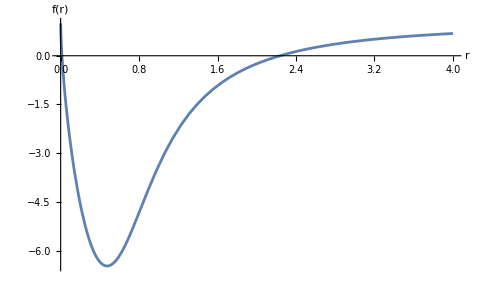

```mathematica
graphf3=Plot[{f3,f32},{r,0,4},AxesLabel->{"r","f(r)"},PlotRange->All]
```

```mathematica
Export["f3.png",graphf3]
```

f3.png

```mathematica
q=1+r^2/(3 α)-(8 2^(1/3) r^4)/(3 (-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ+√(2048 r^12 α^6+(-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ)^2))^(1/3))+((-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ+√(2048 r^12 α^6+(-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ)^2))^(1/3))/(3 2^(1/3) α^2)==0
```

1+r^2/(3 α)-(8 2^(1/3) r^4)/(3 (-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ+√(2048 r^12 α^6+(-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ)^2))^(1/3))+((-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ+√(2048 r^12 α^6+(-25 r^6 α^3-27 r^2 α^5-27 r^2 α^4 μ)^2))^(1/3))/(3 2^(1/3) α^2)==0

```mathematica
Solve[q,r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-(√(μ-√(-12 α^2+μ^2)))/(√6)},{r→(√(μ-√(-12 α^2+μ^2)))/(√6)},{r→-(√(μ+√(-12 α^2+μ^2)))/(√6)},{r→(√(μ+√(-12 α^2+μ^2)))/(√6)}}

```mathematica
α:=0.03
μ:=1
(√(μ-√(-12 α^2+μ^2)))/(√6)
```

0.0300407

```mathematica
(√(μ+√(-12 α^2+μ^2)))/(√6)
```

0.576568